```mathematica
arr = {{"1.in",1000,1000,100,72434,90050,77867,109512,123281,124543,158393},{"2.in",2000,2341,100,219281,258651,221288,278236,314290,324651,415896},{"3.in",3000,4291,100,305096,497997,421960,509678,567357,601835,718903},{"4.in",4000,7161,100,507548,786524,674210,777439,886904,923153,1138509},{"5.in",5000,11392,100,769683,1163359,1002135,1103307,1250934,1344045,1570660},{"6.in",6000,17622,100,1102418,1565287,1403580,1574247,1807548,1899158,2147708},{"7.in",7000,26775,100,1575104,2098335,1972335,1950356,2196193,2410954,3032634},{"8.in",8000,40198,100,2105101,2752214,2482813,2443380,2778458,3065564,3666278},{"9.in",9000,59849,100,2779265,3634808,3199420,3061014,4823517,4803754,5523266},{"10.in",10000,88582,100,4767244,5596839,4634124,5632624,6114423,7135568,8728865},{"11.in",11000,130553,100,6177080,6747387,6410231,5194887,5715708,6338273,7101224},{"12.in",12000,191821,100,6503609,7514392,7088229,6757668,7419732,8144514,9152403},{"13.in",13000,281218,100,8826118,9890314,9617610,8952039,9838244,10564751,11645550},{"14.in",14000,411633,100,11535320,12744831,12397739,11953820,12477136,13581503,15418073},{"15.in",15000,601874,100,15417801,16812162,16258363,15476410,16622907,17664179,19886974},{"16.in",16000,879413,100,20552749,22134079,21398141,20569163,21728012,22744591,25758619},{"17.in",17000,1284399,100,27852400,29199598,28788292,27409926,28690516,30420895,34817358},{"18.in",18000,1875539,100,38217960,39894015,39102419,37737765,39133876,40757604,46186253},{"19.in",19000,2738742,100,53405566,55778391,54326092,53928102,56180039,56594909,66830808},{"20.in",20000,3999800,100,74623356,75765102,75057979,74297074,76057939,77599811,87277087}
};
```

```mathematica
list = Array[{arr[[#1,3]],arr[[#1,#2+4]]}&,{Length[arr],7}]
```

{{{1498,130807},{1498,139422},{1498,119828},{1498,155224},{1498,170843},{1498,175077},{1498,216664}},{{5997,286412},{5997,410125},{5997,358180},{5997,423060},{5997,465281},{5997,507215},{5997,578263}},{{13495,547550},{13495,754107},{13495,652702},{13495,745419},{13495,852800},{13495,946868},{13495,1050186}},{{23994,926941},{23994,1211463},{23994,1074200},{23994,1157863},{23994,1300364},{23994,1440709},{23994,1563654}},{{37492,1396933},{37492,1711335},{37492,1524733},{37492,1613863},{37492,1872341},{37492,2013884},{37492,2265049}},{{53991,1872121},{53991,2371444},{53991,2103912},{53991,2196345},{53991,2456903},{53991,2708994},{53991,3081724}},{{73489,2367723},{73489,3072536},{73489,2799150},{73489,2767827},{73489,3108936},{73489,3522364},{73489,3991726}},{{95988,3071965},{95988,3744596},{95988,3610745},{95988,3453003},{95988,3938856},{95988,4244514},{95988,4787503}},{{121486,4044960},{121486,4947974},{121486,4359623},{121486,4196810},{121486,4932372},{121486,5291160},{121486,6090963}},{{149985,5042072},{149985,5844175},{149985,5349604},{149985,5308099},{149985,5854461},{149985,6454922},{149985,7078555}},{{181483,5930563},{181483,7091762},{181483,6416875},{181483,6361654},{181483,6942255},{181483,7434819},{181483,8336809}},{{215982,7183849},{215982,8117224},{215982,7614352},{215982,7478594},{215982,8223572},{215982,8973489},{215982,9790518}},{{253480,8401633},{253480,9344211},{253480,9197468},{253480,8753806},{253480,9390633},{253480,10102105},{253480,11515325}},{{293979,9473338},{293979,10822818},{293979,10450554},{293979,9945526},{293979,10963068},{293979,11660473},{293979,13347788}},{{337477,11002201},{337477,12318294},{337477,11760496},{337477,11115483},{337477,11932858},{337477,13012573},{337477,14871208}},{{383976,12329297},{383976,13652624},{383976,13162366},{383976,12333179},{383976,13470104},{383976,14618551},{383976,16676832}},{{433474,13739618},{433474,15212922},{433474,14634644},{433474,13777646},{433474,14998211},{433474,16114325},{433474,18475611}},{{485973,15191876},{485973,16920207},{485973,15985300},{485973,15362695},{485973,16339431},{485973,17667224},{485973,21034548}},{{541471,16777459},{541471,18388790},{541471,17704809},{541471,16777011},{541471,17895991},{541471,19196134},{541471,22944611}},{{599970,18066615},{599970,19968050},{599970,18979814},{599970,18080229},{599970,20111905},{599970,20759659},{599970,26172125}}}

```mathematica
mat = Transpose[list]
```

{{{1498,130807},{5997,286412},{13495,547550},{23994,926941},{37492,1396933},{53991,1872121},{73489,2367723},{95988,3071965},{121486,4044960},{149985,5042072},{181483,5930563},{215982,7183849},{253480,8401633},{293979,9473338},{337477,11002201},{383976,12329297},{433474,13739618},{485973,15191876},{541471,16777459},{599970,18066615}},{{1498,139422},{5997,410125},{13495,754107},{23994,1211463},{37492,1711335},{53991,2371444},{73489,3072536},{95988,3744596},{121486,4947974},{149985,5844175},{181483,7091762},{215982,8117224},{253480,9344211},{293979,10822818},{337477,12318294},{383976,13652624},{433474,15212922},{485973,16920207},{541471,18388790},{599970,19968050}},{{1498,119828},{5997,358180},{13495,652702},{23994,1074200},{37492,1524733},{53991,2103912},{73489,2799150},{95988,3610745},{121486,4359623},{149985,5349604},{181483,6416875},{215982,7614352},{253480,9197468},{293979,10450554},{337477,11760496},{383976,13162366},{433474,14634644},{485973,15985300},{541471,17704809},{599970,18979814}},{{1498,155224},{5997,423060},{13495,745419},{23994,1157863},{37492,1613863},{53991,2196345},{73489,2767827},{95988,3453003},{121486,4196810},{149985,5308099},{181483,6361654},{215982,7478594},{253480,8753806},{293979,9945526},{337477,11115483},{383976,12333179},{433474,13777646},{485973,15362695},{541471,16777011},{599970,18080229}},{{1498,170843},{5997,465281},{13495,852800},{23994,1300364},{37492,1872341},{53991,2456903},{73489,3108936},{95988,3938856},{121486,4932372},{149985,5854461},{181483,6942255},{215982,8223572},{253480,9390633},{293979,10963068},{337477,11932858},{383976,13470104},{433474,14998211},{485973,16339431},{541471,17895991},{599970,20111905}},{{1498,175077},{5997,507215},{13495,946868},{23994,1440709},{37492,2013884},{53991,2708994},{73489,3522364},{95988,4244514},{121486,5291160},{149985,6454922},{181483,7434819},{215982,8973489},{253480,10102105},{293979,11660473},{337477,13012573},{383976,14618551},{433474,16114325},{485973,17667224},{541471,19196134},{599970,20759659}},{{1498,216664},{5997,578263},{13495,1050186},{23994,1563654},{37492,2265049},{53991,3081724},{73489,3991726},{95988,4787503},{121486,6090963},{149985,7078555},{181483,8336809},{215982,9790518},{253480,11515325},{293979,13347788},{337477,14871208},{383976,16676832},{433474,18475611},{485973,21034548},{541471,22944611},{599970,26172125}}}

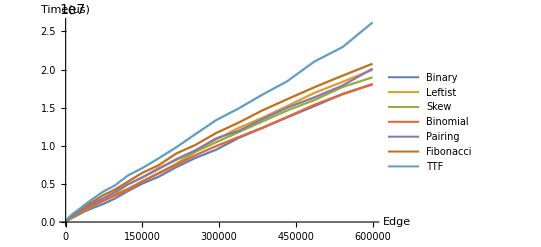

```mathematica
names = {"Binary","Leftist","Skew","Binomial","Pairing","Fibonacci","TTF"};
plots = ListLinePlot[Array[Legended[mat[[#]],names[[#]]]&,7],PlotStyle->Thickness[0.004],AxesLabel->{"Edge","Time(us)"}]
```